```mathematica
(*Clearing workspace*)
Clear["Global`*"]
```

```mathematica
(*Controls function*)
inputFun[t_,t0_,lov_,which_]:=Piecewise@@{Table[{lov[[i,which]],Mod[t,t0 Length[lov]]<t0 i},{i,Length[lov]}]}
```

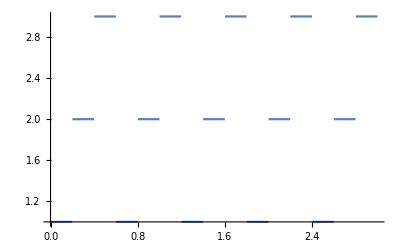

```mathematica
Plot[inputFun[t,0.2,{{1,0},{2,1},{3,2}},1],{t,0,3}]
```

```mathematica
(*List 5 Task 2 initialisation*)
param := {l->1, d->0.5}
(*input :={u1->1,u2->0.5}*)
lov = {{1,0},{0,1},{1,0},{0,-1}}
input :={u1->inputFun[t, 0.2, lov,1],
u2->inputFun[t, 0.2, lov,2]}
equation:={
x'[t]==Cos[theta[t]]*Cos[phi[t]]*u1,
y'[t]==Cos[theta[t]]*Sin[phi[t]]*u1,
phi'[t]==Sin[u1*theta[t]/l],
theta'[t]==u2
}
tmin:=0
tmax:=10
solution=NDSolve[
Join[equation,{x[0]==0,y[0]==0,phi[0]==0,theta[0]==0}]/.param/.input,
{theta[t],phi[t],x[t],y[t]},
{t,tmin,tmax}
]
```

{{1,0},{0,1},{1,0},{0,-1}}

{{theta[t]→InterpolatingFunction[…][t],phi[t]→InterpolatingFunction[…][t],x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

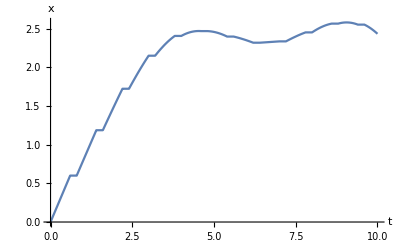

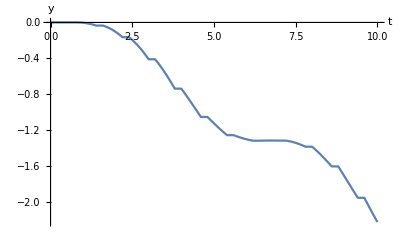

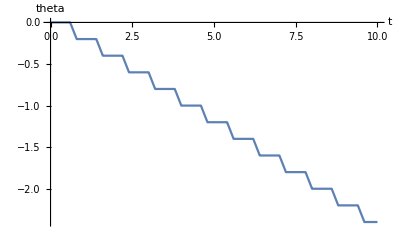

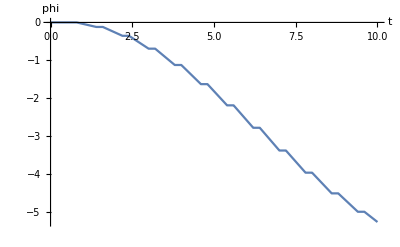

```mathematica
(*List 5 Task plotting 2*)
Plot[x[t]/.solution,{t,tmin,tmax},AxesLabel->{t,x}]
Plot[y[t]/.solution,{t,tmin,tmax},AxesLabel->{t,y}]
Plot[theta[t]/.solution,{t,tmin,tmax},AxesLabel->{t,theta}]
Plot[phi[t]/.solution,{t,tmin,tmax},AxesLabel->{t,phi}]
```

```mathematica
(*Building a car*)
rear[t0_] := Line[{
{x[t]-d*Sin[phi[t]], 
y[t]+d*Cos[phi[t]]},
{x[t]+d*Sin[phi[t]], 
y[t]-d*Cos[phi[t]]}
}/.solution/.param/.{t->t0}]
middle[t0_]:=Line[{
{x[t],
y[t]},
{x[t]+l*Cos[phi[t]],
y[t]+l*Sin[phi[t]]}
}/.solution/.param/.{t->t0}]
front [t0_]:=Line[{
{x[t]+l*Cos[phi[t]]-d*Sin[phi[t]+theta[t]],
y[t]+l*Sin[phi[t]]+d*Cos[phi[t]+theta[t]]},
{x[t]+l*Cos[phi[t]]+d*Sin[phi[t]+theta[t]],
y[t]+l*Sin[phi[t]]-d*Cos[phi[t]+theta[t]]}
}/.solution/.param/.{t->t0}]
```

```mathematica
(*Animation*)
Animate[
Graphics[
{rear[t],middle[t], front[t]},
PlotRange->{{-5,5},{-5,5}}, 
Axes->True
],
{t, tmin, tmax, 0.1},
AnimationRunning->False,
AnimationRate->1
]
```

Line[{{{0.832133,0.561}},{{1.07453,-0.409177}}}]

Line[{{{-Sin[phi[0.2]]+x[0.2]},{Cos[phi[0.2]]+y[0.2]}},{{0.198669+x[0.2]},{-Cos[phi[0.2]]+y[0.2]}}}]